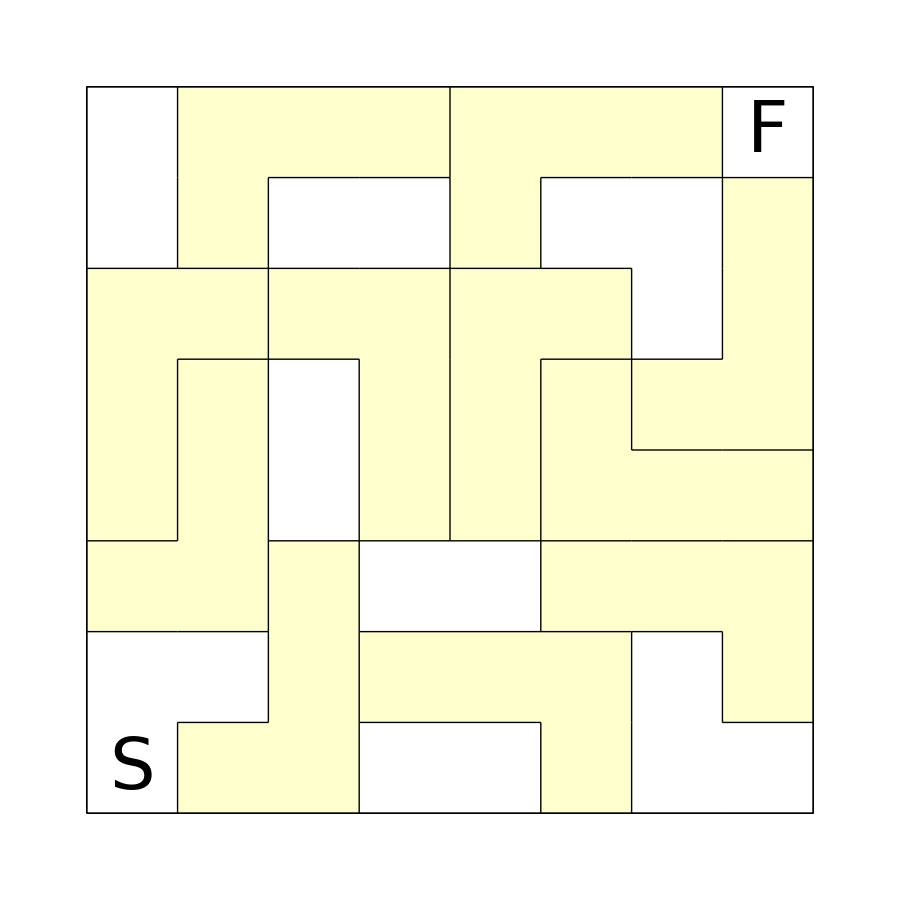

-Graphics-

```mathematica
ref[L_]:=Reverse[L];
rot[L_]:=ref[Transpose[L]];
```

```mathematica
sym[L_]:=Union[{L,rot[L],rot[rot[L]],rot[rot[rot[L]]],
ref[L],ref[rot[L]],ref[rot[rot[L]]],ref[rot[rot[rot[L]]]]}]
```

```mathematica
initialize:=Module[{k,L,n1,n2,pos,loc,shifted},A=ReplacePart[Table[0,{n},{m}],{{1,1},{n,m}}->-1];
For[k=1,k<100,k++,
L=alll[[RandomInteger[{1,Length[alll]}]]];
{n1,n2}=Dimensions[L];
pos=Position[L,1];
loc={RandomInteger[{0,n-n1}],RandomInteger[{0,m-n2}]};
shifted=Map[loc+#&,pos];
If[Union[Extract[A,shifted]]=={0},
A=ReplacePart[A,shifted->Max[Flatten[A]]+1]]];
A=ReplacePart[A,{{1,1},{n,m}}->0];]
```

```mathematica
check0:=Module[{},
stac={{{1,1}}};
solns={};
While[Length[stac]>0&&Length[solns]<2,
cur=First[stac];
stac=Rest[stac];
last=Last[cur];
If[last=={n,m},AppendTo[solns,cur],
poss=Select[Map[last+#&,{{1,0},{-1,0},{0,1},{0,-1}}],1≤#[[1]]≤n&&1≤#[[2]]≤m&&Extract[A,#]==0&&Not[MemberQ[cur,#]]&];
stac=Map[Append[cur,#]&,poss]~Join~stac]]]
```

```mathematica
check1:=Module[{},
stac={{{1,1}}};
solns={};
While[Length[stac]>0&&Length[solns]<2,
cur=First[stac];
stac=Rest[stac];
last=Last[cur];
If[last=={n,m}&&Union[Extract[A,cur]]==Union[Flatten[A]],AppendTo[solns,cur],
visited=Select[Extract[A,cur],#>0&];
poss=Select[Map[last+#&,{{1,0},{-1,0},{0,1},{0,-1}}],1≤#[[1]]≤n&&1≤#[[2]]≤m&&Not[MemberQ[visited,Extract[A,#]]]&&Not[MemberQ[cur,#]]&];
stac=Map[Append[cur,#]&,poss]~Join~stac]]]
```

```mathematica
check2:=Module[{},
stac={{{1,1}}};
solns={};
While[Length[stac]>0&&Length[solns]<2,
cur=First[stac];
stac=Rest[stac];
last=Last[cur];
s=Select[Union[Flatten[A]],#>0&];
If[last=={n,m}&&Sort[Select[Extract[A,cur],#>0&]]==Sort[Flatten[{s,s}]],AppendTo[solns,cur],
visited=Select[Extract[A,cur],#>0&&Count[Extract[A,cur],#]>1&];
poss=Select[Map[last+#&,{{1,0},{-1,0},{0,1},{0,-1}}],1≤#[[1]]≤n&&1≤#[[2]]≤m&&Not[MemberQ[visited,Extract[A,#]]]&&Not[MemberQ[cur,#]]&];
stac=Map[Append[cur,#]&,poss]~Join~stac]]]
```

```mathematica
check3:=Module[{},
stac={{{1,1}}};
solns={};
While[Length[stac]>0&&Length[solns]<2,
cur=First[stac];
stac=Rest[stac];
last=Last[cur];
s=Select[Union[Flatten[A]],#>0&];
If[last=={n,m}&&Sort[Select[Extract[A,cur],#>0&]]==Sort[Flatten[{s,s,s}]],AppendTo[solns,cur],
visited=Select[Extract[A,cur],#>0&&Count[Extract[A,cur],#]>2&];
poss=Select[Map[last+#&,{{1,0},{-1,0},{0,1},{0,-1}}],1≤#[[1]]≤n&&1≤#[[2]]≤m&&Not[MemberQ[visited,Extract[A,#]]]&&Not[MemberQ[cur,#]]&];
stac=Map[Append[cur,#]&,poss]~Join~stac]]]
```

```mathematica
check4:=Module[{},
stac={{{1,1}}};
solns={};
While[Length[stac]>0&&Length[solns]<2,
cur=First[stac];
stac=Rest[stac];
last=Last[cur];
s=Select[Union[Flatten[A]],#>0&];
If[last=={n,m}&&Sort[Select[Extract[A,cur],#>0&]]==Sort[Flatten[{s,s,s,s}]],AppendTo[solns,cur],
visited=Select[Extract[A,cur],#>0&&Count[Extract[A,cur],#]>3&];
poss=Select[Map[last+#&,{{1,0},{-1,0},{0,1},{0,-1}}],1≤#[[1]]≤n&&1≤#[[2]]≤m&&Not[MemberQ[visited,Extract[A,#]]]&&Not[MemberQ[cur,#]]&];
stac=Map[Append[cur,#]&,poss]~Join~stac]]]
```

```mathematica
bord[L_]:=Table[-1,{1},{Length[L[[1]]]}]~Join~L~Join~Table[-1,{1},{Length[L[[1]]]}]
```

```mathematica
border[L_]:=Transpose[bord[Transpose[bord[L]]]]
```

```mathematica
pic[L1_]:=Module[{ii,jj,L,G2,G3},
L=border[L1];
G1=Table[If[L[[ii,jj]]>0,{
          Hue[.17,.2],Rectangle[{ii-2,jj-2},{ii-1,jj-1}]},{}],{ii,
    1,Length[L]},{jj,1,Length[L[[1]]]}];G2={Black,Table[If[L[[ii,jj]]=!=L[[ii+1,jj]],
              Line[{{ii-1,jj-2},{ii-1,jj-1}}],{}],{ii,1,Length[L]-1},{jj,1,
                    Length[L[[1]]]}]};
G3=Table[If[L[[ii,jj]]=!=L[[ii,
            jj+1]],Line[{{ii-2,jj-1},{ii-1,jj-1}}],{}],{ii,1,
              Length[L]},{jj,1,Length[L[[1]]]-1}];
Style[Graphics[Flatten[{G1,G2,G3,Map[Rectangle[#-1,#]&,Position[L1,-2]],Line[{{0,0},{Length[L1],0},{Length[L1],Length[L1[[1]]]},{0,Length[L1[[1]]]},{0,0}}],
Text[Style["S",FontSize->14],{.5,.48}],Text[Style["F",FontSize->14],{n-1/2,m-1/2}]}],ImageSize->{16Length[L1]+1,16Length[L1[[1]]]+1},PlotRange->{{-.05,Length[L]-1.95},{-.05,Length[L[[1]]]-1.95}}],Antialiasing->False]
    ]
```

```mathematica
pic[L1_,soln_]:=Module[{ii,jj,L,G2,G3},
L=border[L1];
G1=Table[If[L[[ii,jj]]>0,{
          Hue[.17,.2],Rectangle[{ii-2,jj-2},{ii-1,jj-1}]},{}],{ii,
    1,Length[L]},{jj,1,Length[L[[1]]]}];G2={Black,Table[If[L[[ii,jj]]=!=L[[ii+1,jj]],
              Line[{{ii-1,jj-2},{ii-1,jj-1}}],{}],{ii,1,Length[L]-1},{jj,1,
                    Length[L[[1]]]}]};
G3=Table[If[L[[ii,jj]]=!=L[[ii,
            jj+1]],Line[{{ii-2,jj-1},{ii-1,jj-1}}],{}],{ii,1,
              Length[L]},{jj,1,Length[L[[1]]]-1}];
Style[Graphics[Flatten[{G1,G2,G3,Map[Rectangle[#-1,#]&,Position[L1,-2]],Line[{{0,0},{Length[L1],0},{Length[L1],Length[L1[[1]]]},{0,Length[L1[[1]]]},{0,0}}],
Red,AbsoluteThickness[2],Line[Map[#-{1/2,1/2}&,soln]]
}],ImageSize->{16Length[L1]+1,16Length[L1[[1]]]+1},PlotRange->{{-.05,Length[L]-1.95},{-.05,Length[L[[1]]]-1.95}}],Antialiasing->False]
    ]
```

```mathematica
ball[1]=sym[{{1,1,1,1,1}}] (* I *)
```

{{{1,1,1,1,1}},{{1},{1},{1},{1},{1}}}

```mathematica
ball[2]=sym[{{1,1,1,1},{1,0,0,0}}] (* L *)
```

{{{0,0,0,1},{1,1,1,1}},{{1,0,0,0},{1,1,1,1}},{{1,1,1,1},{0,0,0,1}},{{1,1,1,1},{1,0,0,0}},{{0,1},{0,1},{0,1},{1,1}},{{1,0},{1,0},{1,0},{1,1}},{{1,1},{0,1},{0,1},{0,1}},{{1,1},{1,0},{1,0},{1,0}}}

```mathematica
ball[3]=sym[{{1,1,1},{1,1,0}}] (* P *)
```

{{{0,1,1},{1,1,1}},{{1,1,0},{1,1,1}},{{1,1,1},{0,1,1}},{{1,1,1},{1,1,0}},{{0,1},{1,1},{1,1}},{{1,0},{1,1},{1,1}},{{1,1},{1,1},{0,1}},{{1,1},{1,1},{1,0}}}

```mathematica
ball[4]=sym[{{1,0,0},{1,1,1},{0,1,0}}] (* R *)
```

{{{0,0,1},{1,1,1},{0,1,0}},{{0,1,0},{0,1,1},{1,1,0}},{{0,1,0},{1,1,0},{0,1,1}},{{0,1,0},{1,1,1},{0,0,1}},{{0,1,0},{1,1,1},{1,0,0}},{{0,1,1},{1,1,0},{0,1,0}},{{1,0,0},{1,1,1},{0,1,0}},{{1,1,0},{0,1,1},{0,1,0}}}

```mathematica
ball[5]=sym[{{1,1,1,0},{0,0,1,1}}] (* S *)
```

{{{0,0,1,1},{1,1,1,0}},{{0,1,1,1},{1,1,0,0}},{{1,1,0,0},{0,1,1,1}},{{1,1,1,0},{0,0,1,1}},{{0,1},{0,1},{1,1},{1,0}},{{0,1},{1,1},{1,0},{1,0}},{{1,0},{1,0},{1,1},{0,1}},{{1,0},{1,1},{0,1},{0,1}}}

```mathematica
ball[6]=sym[{{1,1,1},{0,1,0},{0,1,0}}] (* T *)
```

{{{0,0,1},{1,1,1},{0,0,1}},{{0,1,0},{0,1,0},{1,1,1}},{{1,0,0},{1,1,1},{1,0,0}},{{1,1,1},{0,1,0},{0,1,0}}}

```mathematica
ball[7]=sym[{{1,1,1},{1,0,1}}] (* U *)
```

{{{1,0,1},{1,1,1}},{{1,1,1},{1,0,1}},{{1,1},{0,1},{1,1}},{{1,1},{1,0},{1,1}}}

```mathematica
ball[8]=sym[{{1,0,0},{1,0,0},{1,1,1}}] (* V *)
```

{{{0,0,1},{0,0,1},{1,1,1}},{{1,0,0},{1,0,0},{1,1,1}},{{1,1,1},{0,0,1},{0,0,1}},{{1,1,1},{1,0,0},{1,0,0}}}

```mathematica
ball[9]=sym[{{1,0,0},{1,1,0},{0,1,1}}] (* W *)
```

{{{0,0,1},{0,1,1},{1,1,0}},{{0,1,1},{1,1,0},{1,0,0}},{{1,0,0},{1,1,0},{0,1,1}},{{1,1,0},{0,1,1},{0,0,1}}}

```mathematica
ball[10]=sym[{{0,1,0},{1,1,1},{0,1,0}}] (* X *)
```

{{{0,1,0},{1,1,1},{0,1,0}}}

```mathematica
ball[11]=sym[{{1,1,1,1},{0,0,1,0}}] (* Y *)
```

{{{0,0,1,0},{1,1,1,1}},{{0,1,0,0},{1,1,1,1}},{{1,1,1,1},{0,0,1,0}},{{1,1,1,1},{0,1,0,0}},{{0,1},{0,1},{1,1},{0,1}},{{0,1},{1,1},{0,1},{0,1}},{{1,0},{1,0},{1,1},{1,0}},{{1,0},{1,1},{1,0},{1,0}}}

```mathematica
ball[12]=sym[{{1,0,0},{1,1,1},{0,0,1}}] (* Z *)
```

{{{0,0,1},{1,1,1},{1,0,0}},{{0,1,1},{0,1,0},{1,1,0}},{{1,0,0},{1,1,1},{0,0,1}},{{1,1,0},{0,1,0},{0,1,1}}}

```mathematica
alll=sym[{{1,1,1,1}}]
```

{{{1,1,1,1}},{{1},{1},{1},{1}}}

```mathematica
alll=sym[{{1,1},{1,1}}]
```

{{{1,1},{1,1}}}

```mathematica
For[a=1,a>0,a++,
n=RandomInteger[{4,8}];m=RandomInteger[{n,8}];
alll=sym[{{0,1,0},{1,1,1},{0,1,0}}];
initialize;
check2;
If[Length[solns]==1,Print[pic[A]];Print[pic[A,solns[[1]]]]]]
```

$Aborted

```mathematica
For[a=1,a>0,a++,
n=7;m=7;p=RandomInteger[{1,5}];
alll=sym[{{{1,1,1,1}},{{1,1},{1,1}},{{1,1,1},{1,0,0}},{{1,1,1},{0,1,0}},{{1,1,0},{0,1,1}}}[[p]]];
initialize;
check2;
If[Length[solns]==1,
solns2=solns[[1]];
check1;
If[Length[solns]==1,
Print[pic[A,solns[[1]]]];Print[pic[A,solns2]]]]]
```

$Aborted

```mathematica
For[a=1,a>0,a++,
n=RandomInteger[{4,7}];m=RandomInteger[{Floor[45/n],Floor[60/n]}];
initialize;
check2;
If[Length[solns]==1,Print[pic[A,solns[[1]]]]]]
```

$Aborted

```mathematica
pic[L1_,soln_]:=Module[{ii,jj,L,G2,G3},  (*green solutions *)
L=border[L1];
G0={Table[Line[{{0,h},{Length[L1],h}}],{h,0,Length[L1[[1]]]}],Table[Line[{{h,0},{h,Length[L1[[1]]]}}],{h,0,Length[L1]}]};
G1=Table[If[L[[ii,jj]]>0,{
          Hue[.3],Rectangle[{ii-2,jj-2},{ii-1,jj-1}]},{}],{ii,
    1,Length[L]},{jj,1,Length[L[[1]]]}];
G2={AbsoluteThickness[3],Black,Table[If[L[[ii,jj]]=!=L[[ii+1,jj]]&&L[[ii,jj]]+L[[ii+1,jj]]=!=-1,
              Line[{{ii-1,jj-2},{ii-1,jj-1}}],{}],{ii,1,Length[L]-1},{jj,1,
                    Length[L[[1]]]}]};
G3={AbsoluteThickness[3],Black,Table[If[L[[ii,jj]]=!=L[[ii,
            jj+1]]&&L[[ii,jj]]+L[[ii,
            jj+1]]=!=-1,Line[{{ii-2,jj-1},{ii-1,jj-1}}],{}],{ii,1,
              Length[L]},{jj,1,Length[L[[1]]]-1}]};
Style[Graphics[Flatten[{G0,G1,G2,G3,Map[Rectangle[#-1,#]&,Position[L1,-2]],AbsoluteThickness[1],Line[{{0,0},{Length[L1],0},{Length[L1],Length[L1[[1]]]},{0,Length[L1[[1]]]},{0,0}}],
Red,AbsoluteThickness[3],Line[Map[#-{1/2,1/2}&,soln]]
}],ImageSize->18{Length[L1]+.4,Length[L1[[1]]]+.4}+1,PlotRange->{{-.05,Length[L]-1.95},{-.05,Length[L[[1]]]-1.95}}],Antialiasing->False]
    ]
```

## I5 8x8

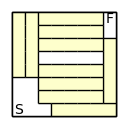

-Graphics-

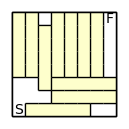

-Graphics-

## L5 8x8

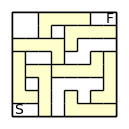

-Graphics-

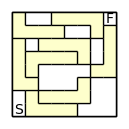

-Graphics-

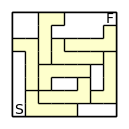

-Graphics-

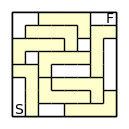

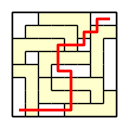

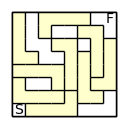

-Graphics-

## P5 8x8

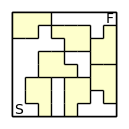

-Graphics-

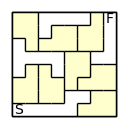

-Graphics-

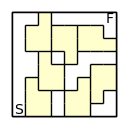

-Graphics-

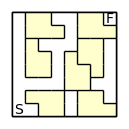

-Graphics-

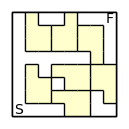

-Graphics-

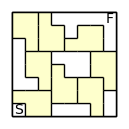

-Graphics-

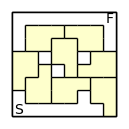

-Graphics-

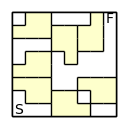

-Graphics-

## R5 8x8

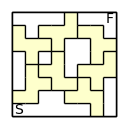

-Graphics-

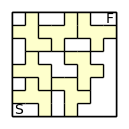

-Graphics-

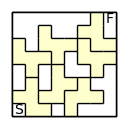

-Graphics-

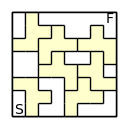

-Graphics-

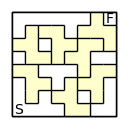

-Graphics-

## S5 8x8

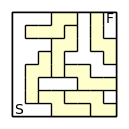

-Graphics-

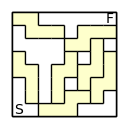

-Graphics-

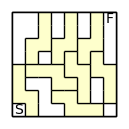

-Graphics-

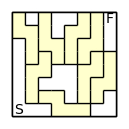

-Graphics-

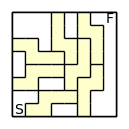

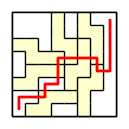

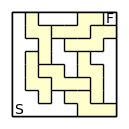

-Graphics-

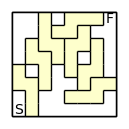

-Graphics-

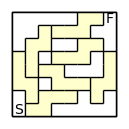

-Graphics-

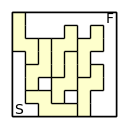

-Graphics-

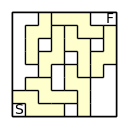

-Graphics-

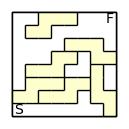

-Graphics-

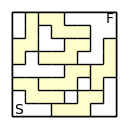

-Graphics-

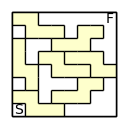

-Graphics-

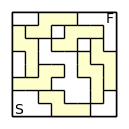

-Graphics-

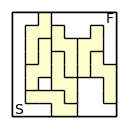

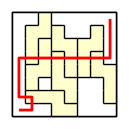

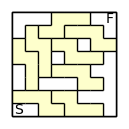

-Graphics-

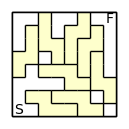

-Graphics-

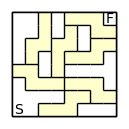

-Graphics-

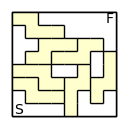

-Graphics-

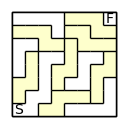

-Graphics-

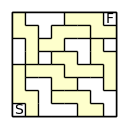

-Graphics-

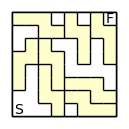

-Graphics-

## T5 8x8

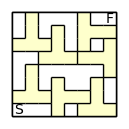

-Graphics-

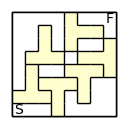

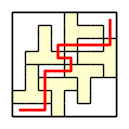

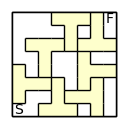

-Graphics-

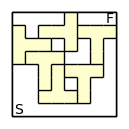

-Graphics-

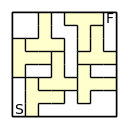

-Graphics-

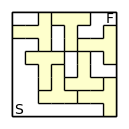

-Graphics-

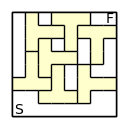

-Graphics-

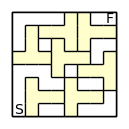

-Graphics-

## U5 8x8

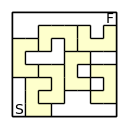

-Graphics-

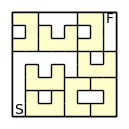

-Graphics-

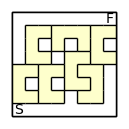

-Graphics-

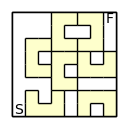

-Graphics-

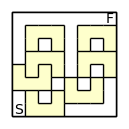

-Graphics-

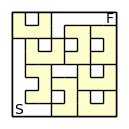

-Graphics-

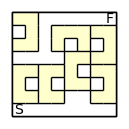

-Graphics-

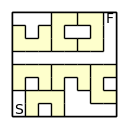

-Graphics-

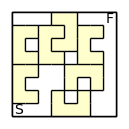

-Graphics-

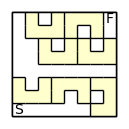

-Graphics-

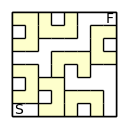

-Graphics-

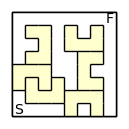

-Graphics-

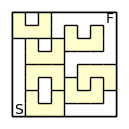

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«65 more identical outputs»

## V5 8x8

-Graphics-

-Graphics-

-Graphics-

«29 more identical outputs»

## W5 8x8

-Graphics-

-Graphics-

-Graphics-

«79 more identical outputs»

## X5 8x8

-Graphics-

-Graphics-

-Graphics-

«351 more identical outputs»

## Y5 8x8

-Graphics-

-Graphics-

-Graphics-

«103 more identical outputs»

## Z5 8x8

-Graphics-

-Graphics-

-Graphics-

«31 more identical outputs»

## L4 6x6

-Graphics-

-Graphics-

-Graphics-

«81 more identical outputs»

## L4 7x7

-Graphics-

-Graphics-

-Graphics-

«45 more identical outputs»

## L4 8x8

-Graphics-

-Graphics-

-Graphics-

«53 more identical outputs»

## L4 10x10

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

## O4 7x7

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

## O4 8x8

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

## O4 9x9

-Graphics-

-Graphics-

-Graphics-

«19 more identical outputs»

## O4 10x10

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

## T4 7x7

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

## T4 8x8

-Graphics-

-Graphics-

-Graphics-

«25 more identical outputs»

## T4 9x9

-Graphics-

-Graphics-

-Graphics-

«35 more identical outputs»

## T4 10x10

-Graphics-

-Graphics-

-Graphics-

«31 more identical outputs»

## I4 7x7

-Graphics-

-Graphics-

-Graphics-

«19 more identical outputs»

## I4 8x8

-Graphics-

-Graphics-

-Graphics-

«25 more identical outputs»

## I4 9x9

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

## I4 10x10

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

## S4 7x7

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

## S4 8x8

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

## S4 9x9

-Graphics-

-Graphics-

-Graphics-

«29 more identical outputs»

## S4 10x10

-Graphics-

-Graphics-

-Graphics-

«17 more identical outputs»

## pents 10x10

## I5 10x10

-Graphics-

-Graphics-

-Graphics-

«7 more identical outputs»

## L5 10x10

-Graphics-

-Graphics-

-Graphics-

«45 more identical outputs»

## P5 10x10

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

## R5 10x10

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

## S5 10x10

-Graphics-

-Graphics-

-Graphics-

«13 more identical outputs»

## T5 10x10

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

## U5 10x10

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

## V5 10x10

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

## W5 10x10

-Graphics-

-Graphics-

-Graphics-

«13 more identical outputs»

## X5 10x10

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

## Y5 10x10

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

## Z5 10x10

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

## pents 14x7

## I5 14x7

-Graphics-

-Graphics-

-Graphics-

«77 more identical outputs»

## L5 14x7

-Graphics-

-Graphics-

-Graphics-

«13 more identical outputs»

## P5 14x7

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

## R5 14x7

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

## S5 14x7

-Graphics-

-Graphics-

-Graphics-

«7 more identical outputs»

## T5 14x7

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

## U5 14x7

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

## V5 14x7

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

## W5 14x7

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

## X5 14x7

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

## Y5 14x7

-Graphics-

-Graphics-

-Graphics-

«137 more identical outputs»

## Z5 14x7

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

## pents twice 8x8

## I5 8x8

-Graphics-

-Graphics-

## L5 8x8

## O6 twice

## O6 7x7 twice

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

## O6 8x8 twice

-Graphics-

-Graphics-

-Graphics-

«41 more identical outputs»

$Aborted

$Aborted